```mathematica
TE=Exp[-pi/hb Sqrt[2 mc/D0] (C0-Ez)] Exp[(E0-Ez)/(kB T)]
Integrate[Ez^-.5 TE,Ez]
Integrate[Ez^-.5 TE,{Ez,0,de}]//TraditionalForm
```

ⅇ^(-(√2 (C0-Ez) √(mc/D0) pi)/hb+(E0-Ez)/(kB T))

-(1. ⅇ^(-(1.41421 C0 √(mc/D0) pi)/hb+E0/(kB T)) (Ez (-(1.41421 √(mc/D0) pi)/hb+1/(kB T)))^0.5 Gamma[0.5,Ez (-(1.41421 √(mc/D0) pi)/hb+1/(kB T))])/(Ez^0.5 (-(1.41421 √(mc/D0) pi)/hb+1/(kB T)))

2. de^0.5 ⅇ^(E0/(kB T)-(√2 C0 pi √(mc/D0))/hb) 0.51.5de ((√2 √(mc/D0) pi)/hb-1/(kB T))

```mathematica
(Ez (-(Sqrt[2] √(mc/D0) pi)/hb+1/(kB T)))^0.5/((Ez^0.5) (-(Sqrt[2] √(mc/D0) pi)/hb+1/(kB T)))//PowerExpand
```

1./(-(√2 √mc pi)/(√D0 hb)+1/(kB T))^0.5

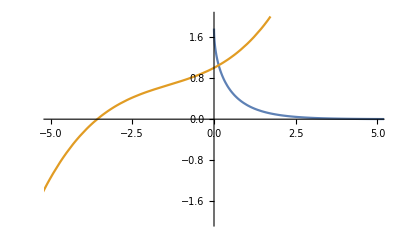

```mathematica
Plot[{Gamma[.5,x],1.+0.3333333333333333 x+0.1 x^2+0.023809523809523808 x^3},{x,-10,10},PlotRange->{{-5,5},{-2,2}}]
```

```mathematica
Series[Hypergeometric1F1[.5,1.5,x],{x,0,3}]
Series[Hypergeometric1F1[.5,1.5,de ((√2 √(mc/D0) pi)/hb-1/(kB T))],{de,0,5}]
```

1.+0.333333 x+0.1 x^2+0.0238095 x^3+O[x]^4

1.+(0.333333 (-1. hb+1.41421 kB √(mc/D0) pi T) de)/(hb kB T)+0.1 ((√2 √(mc/D0) pi)/hb-1/(kB T))^2 de^2+0.0238095 ((√2 √(mc/D0) pi)/hb-1/(kB T))^3 de^3+0.00462963 ((√2 √(mc/D0) pi)/hb-1/(kB T))^4 de^4+0.000757576 ((√2 √(mc/D0) pi)/hb-1/(kB T))^5 de^5+O[de]^6

1.77245+x^0.5 ((-2.+0. ⅈ)+(0.666667+0. ⅈ) x-(0.2+0. ⅈ) x^2+(0.047619+0. ⅈ) x^3-(0.00925926+0. ⅈ) x^4+(0.00151515+0. ⅈ) x^5)

1.77245+((-2.+0. ⅈ)+(0.666667+0. ⅈ) x) x^0.5

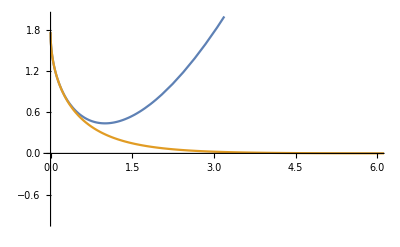

```mathematica
Series[Gamma[.5,x],{x,0,1}]//Normal
Plot[{%,Gamma[.5,x]},{x,0,10},PlotRange->{{0,6},{-1,2}}]
```

```mathematica
1/
```

```mathematica
Gamma[.5,0]
```

1.77245

```mathematica
A=k ((vbi-(vgs-wgc+wfb)) (1-Exp[-gm L])+vds)/(Exp[gm L]-Exp[-gm L]);
B=k ((vbi-(vgs-wgc+wfb)) (Exp[gm L]-1)-vds)/(Exp[gm L]-Exp[-gm L]);
En=Eq0-e (vgs-wgc+wfb)+F (A Exp[gm z]+B Exp[-gm z]);
D[En,vgs]/.z->0
D[En,vgs]/.z->0//Simplify
```

-e+F (((-1+ⅇ^(-gm L)) k)/(-ⅇ^(-gm L)+ⅇ^(gm L))+((1-ⅇ^(gm L)) k)/(-ⅇ^(-gm L)+ⅇ^(gm L)))

-e-F k

```mathematica
zmx=1/(2 gm) Log[B/A]
```

Log[(-vds+(-1+ⅇ^(gm L)) (vbi-vgs-wfb+wgc))/(vds+(1-ⅇ^(-gm L)) (vbi-vgs-wfb+wgc))]/(2 gm)

```mathematica
Ezmx=En/.z->zmx//Simplify
```

Eq0-e (vgs+wfb-wgc)+(ⅇ^(gm L) F k (-vds+(-1+ⅇ^(gm L)) (vbi-vgs-wfb+wgc)))/((-1+ⅇ^(2 gm L)) √((-vds+(-1+ⅇ^(gm L)) (vbi-vgs-wfb+wgc))/(vds+(1-ⅇ^(-gm L)) (vbi-vgs-wfb+wgc))))+(ⅇ^(gm L) F k (vds+(1-ⅇ^(-gm L)) (vbi-vgs-wfb+wgc)) √((-vds+(-1+ⅇ^(gm L)) (vbi-vgs-wfb+wgc))/(vds+(1-ⅇ^(-gm L)) (vbi-vgs-wfb+wgc))))/(-1+ⅇ^(2 gm L))

```mathematica
Ezer=En/.z->0//Simplify
```

Eq0-e (vgs+wfb-wgc)+F k (vbi-vgs-wfb+wgc)

```mathematica
Ezmx-Ezer//Simplify
```

F k (-vbi+vgs+wfb-wgc+(ⅇ^(gm L) (-vds+(-1+ⅇ^(gm L)) (vbi-vgs-wfb+wgc)))/((-1+ⅇ^(2 gm L)) √((-vds+(-1+ⅇ^(gm L)) (vbi-vgs-wfb+wgc))/(vds+(1-ⅇ^(-gm L)) (vbi-vgs-wfb+wgc))))+(ⅇ^(gm L) (vds+(1-ⅇ^(-gm L)) (vbi-vgs-wfb+wgc)) √((-vds+(-1+ⅇ^(gm L)) (vbi-vgs-wfb+wgc))/(vds+(1-ⅇ^(-gm L)) (vbi-vgs-wfb+wgc))))/(-1+ⅇ^(2 gm L)))

```mathematica
D[zmx,vgs]//Simplify//TraditionalForm
```

(vds (ⅇ^(2 gm L)-1))/(2 gm (vbi (-ⅇ^(gm L))+(ⅇ^(gm L)-1) (vgs+wfb-wgc)+vbi+vds) (vbi (ⅇ^(gm L)-1)+ⅇ^(gm L) (vds-vgs-wfb+wgc)+vgs+wfb-wgc))

```mathematica
D[1/(2 gm) Log[BB[vgs]/AA[vgs]],vgs]
1/(2 gm) (D[B,vgs]/B-D[A,vgs]/A)//Simplify
```

(AA[vgs] (-(BB[vgs] AA'[vgs])/AA[vgs]^2+BB'[vgs]/AA[vgs]))/(2 gm BB[vgs])

(-(-1+ⅇ^(-gm L))/(vds+(1-ⅇ^(-gm L)) (vbi-vgs-wfb+wgc))+(1-ⅇ^(gm L))/(-vds+(-1+ⅇ^(gm L)) (vbi-vgs-wfb+wgc)))/(2 gm)

```mathematica
D[Ezmx-Ezer,vgs]//Simplify
```

1/2 F k (2-(2 ⅇ^(gm L))/((1+ⅇ^(gm L)) √(-(vds-(-1+ⅇ^(gm L)) (vbi-vgs-wfb+wgc))/(vds+(1-ⅇ^(-gm L)) (vbi-vgs-wfb+wgc))))-(2 √(-(vds-(-1+ⅇ^(gm L)) (vbi-vgs-wfb+wgc))/(vds+(1-ⅇ^(-gm L)) (vbi-vgs-wfb+wgc))))/(1+ⅇ^(gm L)))

```mathematica
D[Ezer,vgs]//Simplify
```

-e-F k

```mathematica
D[(Ezmx-Ezer)/zmx^2,vgs]//Simplify
```

-((4 F gm^2 k (2 (ⅇ^(-gm L) vds-ⅇ^(gm L) vds) (2 ⅇ^(gm L) (vds-(-1+ⅇ^(gm L)) (vbi-vgs-wfb+wgc))+(-1+ⅇ^(2 gm L)) (vbi-vgs-wfb+wgc) √(-(vds-(-1+ⅇ^(gm L)) (vbi-vgs-wfb+wgc))/(vds+(1-ⅇ^(-gm L)) (vbi-vgs-wfb+wgc))))-(vds-(-1+ⅇ^(gm L)) (vbi-vgs-wfb+wgc)) (ⅇ^(gm L) (1-ⅇ^(gm L)) (vds+(1-ⅇ^(-gm L)) (vbi-vgs-wfb+wgc))+ⅇ^(gm L) (1-ⅇ^(-gm L)) (vds-(-1+ⅇ^(gm L)) (vbi-vgs-wfb+wgc))+((1-ⅇ^(2 gm L)) (vds-(-1+ⅇ^(gm L)) (vbi-vgs-wfb+wgc)))/(√(-(vds-(-1+ⅇ^(gm L)) (vbi-vgs-wfb+wgc))/(vds+(1-ⅇ^(-gm L)) (vbi-vgs-wfb+wgc))))) Log[(-vds+(-1+ⅇ^(gm L)) (vbi-vgs-wfb+wgc))/(vds+(1-ⅇ^(-gm L)) (vbi-vgs-wfb+wgc))]))/((1-ⅇ^(2 gm L)) (vds+(1-ⅇ^(-gm L)) (vbi-vgs-wfb+wgc))^2 (-(vds-(-1+ⅇ^(gm L)) (vbi-vgs-wfb+wgc))/(vds+(1-ⅇ^(-gm L)) (vbi-vgs-wfb+wgc)))^(3/2) Log[(-vds+(-1+ⅇ^(gm L)) (vbi-vgs-wfb+wgc))/(vds+(1-ⅇ^(-gm L)) (vbi-vgs-wfb+wgc))]^3))

```mathematica
Exp[gm 1/(1 gm) Log[B/A]]
```

(-vds+(-1+ⅇ^(gm L)) (vbi-vgs-wfb+wgc))/(vds+(1-ⅇ^(-gm L)) (vbi-vgs-wfb+wgc))

```mathematica
D[((Sqrt[AA[vgs]]-Sqrt[BB[vgs]])/(Log[BB[vgs]]-Log[AA[vgs]]))^2,vgs]//PowerExpand
```

-(2 (√AA[vgs]-√BB[vgs])^2 (-AA'[vgs]/AA[vgs]+BB'[vgs]/BB[vgs]))/(-Log[AA[vgs]]+Log[BB[vgs]])^3+(2 (√AA[vgs]-√BB[vgs]) (AA'[vgs]/(2 √AA[vgs])-BB'[vgs]/(2 √BB[vgs])))/(-Log[AA[vgs]]+Log[BB[vgs]])^2

```mathematica
D[(Sqrt[AA[vgs]]-Sqrt[BB[vgs]])^2,vgs]//Simplify
```

(1-(√BB[vgs])/(√AA[vgs])) AA'[vgs]+(1-(√AA[vgs])/(√BB[vgs])) BB'[vgs]

```mathematica
D[Exp[-pi/hb Sqrt[(2 mc)/D0[vgs]] C0[vgs]+E0[vgs]/(k T)]/(-pi/hb Sqrt[(2 mc)/D0[vgs]]+1/(k T)) Gamma[.5,-pi/hb Sqrt[(2 mc)/D0[vgs]] Ez+Ez/(k T)],vgs]
```

-(ⅇ^(-Ez/(k T)+(√2 Ez pi √(mc/D0[vgs]))/hb-(√2 pi C0[vgs] √(mc/D0[vgs]))/hb+E0[vgs]/(k T)) Ez mc pi D0'[vgs])/(√2 hb (1/(k T)-(√2 pi √(mc/D0[vgs]))/hb) (Ez/(k T)-(√2 Ez pi √(mc/D0[vgs]))/hb)^0.5 √(mc/D0[vgs]) D0[vgs]^2)-(ⅇ^(-(√2 pi C0[vgs] √(mc/D0[vgs]))/hb+E0[vgs]/(k T)) mc pi Gamma[0.5,Ez/(k T)-(√2 Ez pi √(mc/D0[vgs]))/hb] D0'[vgs])/(√2 hb (1/(k T)-(√2 pi √(mc/D0[vgs]))/hb)^2 √(mc/D0[vgs]) D0[vgs]^2)+1/(1/(k T)-(√2 pi √(mc/D0[vgs]))/hb)ⅇ^(-(√2 pi C0[vgs] √(mc/D0[vgs]))/hb+E0[vgs]/(k T)) Gamma[0.5,Ez/(k T)-(√2 Ez pi √(mc/D0[vgs]))/hb] (-(√2 pi √(mc/D0[vgs]) C0'[vgs])/hb+(mc pi C0[vgs] D0'[vgs])/(√2 hb √(mc/D0[vgs]) D0[vgs]^2)+E0'[vgs]/(k T))

```mathematica
D[Gamma[.5,-pi/hb Sqrt[(2 mc)/D0[vgs]] Ez+Ez/(k T)]/.Ez->F (Sqrt[A]-Sqrt[B])^2,vgs]
Gamma[.5,-pi/hb Sqrt[(2 mc)/D0[vgs]] Ez+Ez/(k T)]/.Ez->0
```

-((ⅇ^(-(F (√((k (vds+(1-ⅇ^(-gm L)) (vbi-vgs-wfb+wgc)))/(-ⅇ^(-gm L)+ⅇ^(gm L)))-√((k (-vds+(-1+ⅇ^(gm L)) (vbi-vgs-wfb+wgc)))/(-ⅇ^(-gm L)+ⅇ^(gm L))))^2)/(k T)+(√2 F pi (√((k (vds+(1-ⅇ^(-gm L)) (vbi-vgs-wfb+wgc)))/(-ⅇ^(-gm L)+ⅇ^(gm L)))-√((k (-vds+(-1+ⅇ^(gm L)) (vbi-vgs-wfb+wgc)))/(-ⅇ^(-gm L)+ⅇ^(gm L))))^2 √(mc/D0[vgs]))/hb) (1/(k T)2 F (((-1+ⅇ^(-gm L)) k)/(2 (-ⅇ^(-gm L)+ⅇ^(gm L)) √((k (vds+(1-ⅇ^(-gm L)) (vbi-vgs-wfb+wgc)))/(-ⅇ^(-gm L)+ⅇ^(gm L))))-((1-ⅇ^(gm L)) k)/(2 (-ⅇ^(-gm L)+ⅇ^(gm L)) √((k (-vds+(-1+ⅇ^(gm L)) (vbi-vgs-wfb+wgc)))/(-ⅇ^(-gm L)+ⅇ^(gm L))))) (√((k (vds+(1-ⅇ^(-gm L)) (vbi-vgs-wfb+wgc)))/(-ⅇ^(-gm L)+ⅇ^(gm L)))-√((k (-vds+(-1+ⅇ^(gm L)) (vbi-vgs-wfb+wgc)))/(-ⅇ^(-gm L)+ⅇ^(gm L))))-1/hb 2 √2 F pi (((-1+ⅇ^(-gm L)) k)/(2 (-ⅇ^(-gm L)+ⅇ^(gm L)) √((k (vds+(1-ⅇ^(-gm L)) (vbi-vgs-wfb+wgc)))/(-ⅇ^(-gm L)+ⅇ^(gm L))))-((1-ⅇ^(gm L)) k)/(2 (-ⅇ^(-gm L)+ⅇ^(gm L)) √((k (-vds+(-1+ⅇ^(gm L)) (vbi-vgs-wfb+wgc)))/(-ⅇ^(-gm L)+ⅇ^(gm L))))) (√((k (vds+(1-ⅇ^(-gm L)) (vbi-vgs-wfb+wgc)))/(-ⅇ^(-gm L)+ⅇ^(gm L)))-√((k (-vds+(-1+ⅇ^(gm L)) (vbi-vgs-wfb+wgc)))/(-ⅇ^(-gm L)+ⅇ^(gm L)))) √(mc/D0[vgs])+(F mc pi (√((k (vds+(1-ⅇ^(-gm L)) (vbi-vgs-wfb+wgc)))/(-ⅇ^(-gm L)+ⅇ^(gm L)))-√((k (-vds+(-1+ⅇ^(gm L)) (vbi-vgs-wfb+wgc)))/(-ⅇ^(-gm L)+ⅇ^(gm L))))^2 D0'[vgs])/(√2 hb √(mc/D0[vgs]) D0[vgs]^2)))/((F (√((k (vds+(1-ⅇ^(-gm L)) (vbi-vgs-wfb+wgc)))/(-ⅇ^(-gm L)+ⅇ^(gm L)))-√((k (-vds+(-1+ⅇ^(gm L)) (vbi-vgs-wfb+wgc)))/(-ⅇ^(-gm L)+ⅇ^(gm L))))^2)/(k T)-(√2 F pi (√((k (vds+(1-ⅇ^(-gm L)) (vbi-vgs-wfb+wgc)))/(-ⅇ^(-gm L)+ⅇ^(gm L)))-√((k (-vds+(-1+ⅇ^(gm L)) (vbi-vgs-wfb+wgc)))/(-ⅇ^(-gm L)+ⅇ^(gm L))))^2 √(mc/D0[vgs]))/hb)^0.5)

1.77245

```mathematica
Integrate[ez^(-.5) (1+Exp[en0+ez])^(-1),ez]
Integrate[ez^(-.5) (1+Exp[en0+ez])^(-1),{ez,0,Infinity}]//Simplify
```

∫1/((1+ⅇ^(en0+ez)) ez^0.5)ⅆez

-1.77245 PolyLog[0.5,-ⅇ^-en0]

```mathematica
Integrate[ez^(-.5)/(1+Exp[en0+ez]),{ez,0,Infinity}]
```

-1.77245 PolyLog[0.5,-ⅇ^-en0]